# Tangent Space

## Environment

```mathematica
SetDirectory[NotebookDirectory[]];
SetOptions[EvaluationNotebook[],CellContext->Notebook];
Off[Solve::ifun];
```

## Boxes

```mathematica
MakeBoxes[θM,StandardForm]:=SuperscriptBox["θ","M"];
MakeExpression[SuperscriptBox["θ","M"],StandardForm]:=MakeExpression["θM",StandardForm];
MakeBoxes[τ1,StandardForm]:=SubscriptBox["τ","1"];
MakeExpression[SubscriptBox["τ","1"],StandardForm]:=MakeExpression["τ1",StandardForm];
MakeBoxes[τ1B,StandardForm]:=SubsuperscriptBox["τ","1","B"];
MakeExpression[SubsuperscriptBox["τ","1","B"],StandardForm]:=MakeExpression["τ1B",StandardForm];
MakeBoxes[τ1C,StandardForm]:=SubsuperscriptBox["τ","1","C"];
MakeExpression[SubsuperscriptBox["τ","1","C"],StandardForm]:=MakeExpression["τ1C",StandardForm];
MakeBoxes[τ1G,StandardForm]:=SubsuperscriptBox["τ","1","G"];
MakeExpression[SubsuperscriptBox["τ","1","G"],StandardForm]:=MakeExpression["τ1G",StandardForm];
MakeBoxes[τ1R,StandardForm]:=SubsuperscriptBox["τ","1","R"];
MakeExpression[SubsuperscriptBox["τ","1","R"],StandardForm]:=MakeExpression["τ1R",StandardForm];
MakeBoxes[τB,StandardForm]:=SuperscriptBox["τ","B"];
MakeExpression[SuperscriptBox["τ","B"],StandardForm]:=MakeExpression["τB",StandardForm];
MakeBoxes[τR,StandardForm]:=SuperscriptBox["τ","R"];
MakeExpression[SuperscriptBox["τ","R"],StandardForm]:=MakeExpression["τR",StandardForm];
MakeBoxes[a1,StandardForm]:=SubscriptBox["a","1"];
MakeExpression[SubscriptBox["a","1"],StandardForm]:=MakeExpression["a1",StandardForm];
MakeBoxes[dτR,StandardForm]:=SuperscriptBox["dτ","R"];
MakeExpression[SuperscriptBox["dτ","R"],StandardForm]:=MakeExpression["dτR",StandardForm];
MakeBoxes[dτB,StandardForm]:=SuperscriptBox["dτ","B"];
MakeExpression[SuperscriptBox["dτ","B"],StandardForm]:=MakeExpression["dτB",StandardForm];
MakeBoxes[dxB,StandardForm]:=SuperscriptBox["dx","B"];
MakeExpression[SuperscriptBox["dx","B"],StandardForm]:=MakeExpression["dxB",StandardForm];
MakeBoxes[dxM,StandardForm]:=SuperscriptBox["dx","M"];
MakeExpression[SuperscriptBox["dx","M"],StandardForm]:=MakeExpression["dxM",StandardForm];
MakeBoxes[tangentVelocity,StandardForm]:=SubscriptBox["V","τ"];
MakeExpression[SubscriptBox["V","τ"],StandardForm]:=MakeExpression["tangentVelocity",StandardForm];
MakeBoxes[v1,StandardForm]:=SubscriptBox["v","1"];
MakeExpression[SubscriptBox["v","1"],StandardForm]:=MakeExpression["v1",StandardForm];
MakeBoxes[v1R,StandardForm]:=SubsuperscriptBox["v","1","R"];
MakeExpression[SubsuperscriptBox["v","1","R"],StandardForm]:=MakeExpression["v1R",StandardForm];
MakeBoxes[v1B,StandardForm]:=SubsuperscriptBox["v","1","B"];
MakeExpression[SubsuperscriptBox["v","1","B"],StandardForm]:=MakeExpression["v1B",StandardForm];
MakeBoxes[xM,StandardForm]:=SuperscriptBox["x","M"];
MakeExpression[SuperscriptBox["x","M"],StandardForm]:=MakeExpression["xM",StandardForm];
MakeBoxes[y1R,StandardForm]:=SubsuperscriptBox["y","1","R"];
MakeExpression[SubsuperscriptBox["y","1","R"],StandardForm]:=MakeExpression["y1R",StandardForm];
MakeBoxes[y1B,StandardForm]:=SubsuperscriptBox["y","1","B"];
MakeExpression[SubsuperscriptBox["y","1","B"],StandardForm]:=MakeExpression["y1B",StandardForm];
MakeBoxes[yM,StandardForm]:=SuperscriptBox["y","M"];
MakeExpression[SuperscriptBox["y","M"],StandardForm]:=MakeExpression["yM",StandardForm];
```

## Units

```mathematica
s=1;
m=1;
cm=0.01 m;
kg=1;
g=0.001 kg;
J=(kg m^2)/s^2;
K=1;
km=1000 m;
yr=60 60 24 365.25 s;
kyr=1000 yr;
Myr=1000 kyr;
Gyr=1000 Myr;
pc=3.08567758 10^13 km;
kpc=1000 pc;
Mpc=1000 kpc;
Gpc=1000 Mpc;
```

## Constants

```mathematica
G=6.67408 10^-11 m^3/(kg s^2);
ℏ=6.62607004 10^-34 J s;
Subscript[k, B]=1.380649 10^-23 J/K;
Subscript[a, B]=(8 π^5 Subscript[k, B]^4)/(15 ℏ^3 Subscript[c, 3]^3)J/(m^3 K^4);
Subscript[η, 0]=Subscript[η, t][Subscript[t, 0]];
h=2/(100 Subscript[t, 0])Mpc/km;
Subscript[H, 0]=h 100 km/(s Mpc);
Subscript[T, 0]=2.7255 K;
θ100=1.0411;
Subscript[A, He]=0.25;
Subscript[A, H]=0.75;
Subscript[m, He]=6.6464764 10^-27 kg;
Subscript[m, H]=1.6735575 10^-27 kg;
Subscript[σ, T]=6.6524 10^-29 m^2;
Subscript[ρ, γ]=(Subscript[a, B] Subscript[T, 0]^4)/Subscript[c, 3]^2 kg/m^3;
```

## Clear Variables

```mathematica
ClearAll[τ,τ^R,τ^B,dτ^R,dτ^B]
ClearAll[θ^M]
ClearAll[x^M,dx^B,dx^M]
ClearAll[y^M,Subscript[y, 1]^R,Subscript[y, 1]^B]
ClearAll[Subscript[V, τ],Subscript[v, 1]^R,Subscript[v, 1]^B]
ClearAll[Subscript[τ, 1],Subscript[a, 1],Subscript[v, 1]]
```

## The metric tensor (with the assumption of simultaneity)

### The Two-Dimensional Metric Formula

```mathematica
y^M=(ⅈ Subscript[y, 1]^R τ^R+ⅈ Subscript[y, 1]^B τ^B+ⅈ τ^R ⅈ τ^B) Cos[θ^M]
```

(ⅈ y_1^B τ^B+ⅈ y_1^R τ^R-τ^B τ^R) Cos[θ^M]

```mathematica
Subscript[y, 1]^R=-(ⅈ 2 Subscript[v, 1]^R)/Subscript[a, 1];
Subscript[y, 1]^B=-(ⅈ 2 Subscript[v, 1]^B)/Subscript[a, 1];
x^M=FullSimplify[Subscript[a, 1]/2 y^M];
```

### Tangent Velocity

```mathematica
τ^R=τ;τ^B=τ;
Subscript[v, 1]^R=Subscript[v, 1]/2;Subscript[v, 1]^B=Subscript[v, 1]/2;
θ^M=0;
x^M;
Subscript[V, τ]=Simplify[ⅈ D[x^M, τ]]
```

ⅈ (v_1-a_1 τ)

### Now that we have the tangent velocity in the reference frame, allow θ^M to vary .

```mathematica
ClearAll[θ^M]
```

```mathematica
dx^B=dx^B/.Solve[dx^B/dτ^B==Subscript[V, τ],dx^B]⟦1⟧
dτ^B=dτ^B/.Solve[dτ/dτ^B==Cos[θ^M],dτ^B]⟦1⟧
```

ⅈ dτ^B (v_1-a_1 τ)

dτ Sec[θ^M]

### The tangent velocity is the dot product of the meter and second velocities.

```mathematica
dx^M=dx^M/.FullSimplify[Solve[Subscript[V, τ]^2==(dx^B/dτ)^2+(dx^M/dτ)^2,dx^M]]⟦2⟧
```

dτ (v_1-a_1 τ) √(Tan[θ^M]^2)

### The angle between time axes is a function of relative velocity: dx^M/ⅈdτ^B.

```mathematica
θ^M=θ^M/.Solve[dx^M/(ⅈ dτ^B)==-ⅈ v,θ^M]⟦1⟧
```

ArcSin[v/(v_1-a_1 τ)]

### Arbitrary time vs. Reference Time

```mathematica
dτ^B
```

dτ/(√(1-v^2/(v_1-a_1 τ)^2))

### Arbitrary time vs. Relative Velocity

```mathematica
Subscript[v, 1]=2.663617×10^8 m/s;
Subscript[a, 1]=3.4630912×10^-11 m/s^2;
Subscript[τ, 1]=9.653442×10^17 s;
```

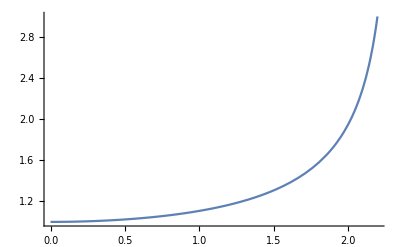

```mathematica
Plot[{dτ^B/.{dτ->1,τ->Subscript[τ, 1]}},{v,0,Subscript[v, 1]-Subscript[a, 1] Subscript[τ, 1]},PlotRange->{3,0}]
```